# Algorithmic Dynamics of Emergent Patterns and Colliding Particles in the Game of Life

Hector Zenil, Narsis A. Kiani and Jesper Tegnér

Supporting sources:

```mathematica
Import["http://wwwhomes.uni-bielefeld.de/achim/freq_top_life.html","Elements"]
```

{Data,FullData,Hyperlinks,ImageLinks,Images,Plaintext,Source,Title,XMLObject}

Required data: (update the locations)

```mathematica
SetDirectory["/Users/hectorzenil/Desktop/BDM/"]
```

/Users/hectorzenil/Desktop/BDM

```mathematica
reducedD2=<<"squares2Dsize1to4.m";
```

```mathematica
Table[With[{sq=reducedD2[[nS]]},HashSquares[sq[[1]]]=sq[[2]]],{nS,Length@reducedD2}];
```

```mathematica
BDM[array_,dim_Integer:4]:=If[TrueQ[Min[Dimensions[array]]<dim],BDM[array,Min[Dimensions[array]]],First[Block[{part=Partition[array,{dim,dim}]},Total[{Log[2,#[[2]]]+#[[1]]}&/@({HashSquares[#[[1]]],#[[2]]}&/@Tally[Flatten[part,1]])]]]]
```

```mathematica
Clear[reducedD2]
```

```mathematica
ArrayTrim[ca_]:=Module[{vals=Flatten[Position[(Count[#,1])&/@(ca),x_/;x≠0]],restrans=Flatten[Position[(Count[#,1])&/@(Transpose[ca]),x_/;x≠0]]&/@Transpose[ca]},#[[Min[restrans];;Max[restrans]]]&/@ca[[Min[vals];;Max[vals]]]]
```

```mathematica
CoarseGrain[array_]:=Flatten/@((SplitBy/@Transpose[List/@Map[Flatten,(((SplitBy/@ArrayTrim[ImageData[Binarize@ColorNegate@array]]))/.{{1,___}->1,{0,0,___}->{0,0,0},{0}->0}),{1}]])/.{{1,___}->1,{0,0,___}->{0,0,0},{0}->0})
```

```mathematica
GoLmotifs=Rest[Import["http://wwwhomes.uni-bielefeld.de/achim/freq_top_life.html","Images"]];
```

```mathematica
GoLdata=Import["http://wwwhomes.uni-bielefeld.de/achim/freq_top_life.html","Source"]
```

```mathematica
bdmGoLmotifs=Map[N@BDM[ArrayTrim@ImageData[ColorNegate@Binarize@#]]&,If[!Head[#]===List,{#},#]&/@GoLmotifs,{2}];
```

```mathematica
entropyGoLmotifs=Map[N@Entropy[ArrayTrim@ImageData[ColorNegate@Binarize@#]]&,If[!Head[#]===List,{#},#]&/@GoLmotifs,{2}];
```

```mathematica
compressGoLmotifs=Map[ByteCount@Compress[ArrayTrim@ImageData[ColorNegate@Binarize@#]]&,If[!Head[#]===List,{#},#]&/@GoLmotifs,{2}];
```

Total number of occurrences:

```mathematica
Total[ToExpression/@(#[[-2]]&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]))]
```

50157774850

Classification by symmetries:

```mathematica
sizes=#[[-7]]&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]);
```

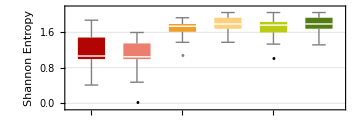
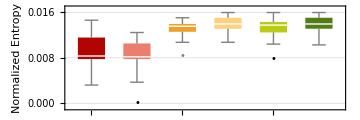

```mathematica
Row[{BoxWhiskerChart[(Flatten/@Map[First,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{entropyGoLmotifs[[ToExpression[#[[1]]]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]),"Outliers",ChartStyle->10,PlotTheme->"Detailed",AspectRatio->1/3,ImageSize->Medium,ChartLabels->{(Style[#,20,Black,Bold]&/@Flatten[Union/@Map[Last,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{ToExpression[#[[1]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]])},FrameLabel->{"",Style["Shannon Entropy",14,Black]}],"   ",BoxWhiskerChart[(Flatten/@Map[First,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{entropyGoLmotifs[[ToExpression[#[[1]]]]]/Total[ImageDimensions[If[Head[#]===List,First@#,#]&@GoLmotifs[[ToExpression[#[[1]]]]]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]),"Outliers",ChartStyle->10,PlotTheme->"Detailed",AspectRatio->1/3,ImageSize->Medium,ChartLabels->{(Style[#,20,Black,Bold]&/@Flatten[Union/@Map[Last,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{ToExpression[#[[1]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]])},FrameLabel->{"",Style["Normalized Entropy",14,Black]}]}]
```

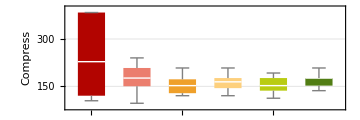
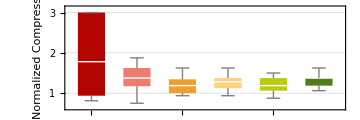

```mathematica
Row[{BoxWhiskerChart[(Flatten/@Map[First,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{compressGoLmotifs[[ToExpression[#[[1]]]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]),"Outliers",ChartStyle->10,PlotTheme->"Detailed",AspectRatio->1/3,ImageSize->Medium,ChartLabels->{(Style[#,20,Black,Bold]&/@Flatten[Union/@Map[Last,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{ToExpression[#[[1]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]])},FrameLabel->{"",Style["Compress",14,Black]}],"   ",BoxWhiskerChart[(Flatten/@Map[First,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{compressGoLmotifs[[ToExpression[#[[1]]]]]/Total[ImageDimensions[If[Head[#]===List,First@#,#]&@GoLmotifs[[ToExpression[#[[1]]]]]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]),"Outliers",ChartStyle->10,PlotTheme->"Detailed",AspectRatio->1/3,ImageSize->Medium,ChartLabels->{(Style[#,20,Black,Bold]&/@Flatten[Union/@Map[Last,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{ToExpression[#[[1]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]])},FrameLabel->{"",Style["Normalized Compress",14,Black]}]}]
```

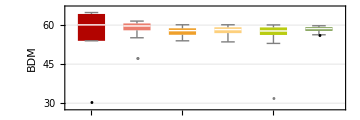
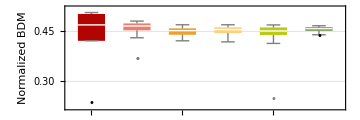

```mathematica
Row@{BoxWhiskerChart[(Flatten/@Map[First,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{bdmGoLmotifs[[ToExpression[#[[1]]]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]),"Outliers",ChartStyle->10,PlotTheme->"Detailed",AspectRatio->1/3,ImageSize->Medium,ChartLabels->{Style[#,20,Black,Bold]&/@Flatten[Union/@Map[Last,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{ToExpression[#[[1]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]]},FrameLabel->{"",Style["BDM",14,Black]},PlotRange->{52,All}],"   ",BoxWhiskerChart[(Flatten/@Map[First,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{bdmGoLmotifs[[ToExpression[#[[1]]]]]/Total[ImageDimensions[If[Head[#]===List,First@#,#]&@GoLmotifs[[ToExpression[#[[1]]]]]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]),"Outliers",ChartStyle->10,PlotTheme->"Detailed",AspectRatio->1/3,ImageSize->Medium,ChartLabels->{Style[#,20,Black,Bold]&/@Flatten[Union/@Map[Last,#[[{1,3,-1,5,-2,4}]]&@GatherBy[SortBy[{ToExpression[#[[1]]],#[[-6]]}&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]),Last],Last],{2}]]},FrameLabel->{"",Style["Normalized BDM",14,Black]},PlotRange->{.40,All}]}
```

Algorithmic Distribution of Patterns in GoL

GoL patterns roughly follow the Universal Distribution

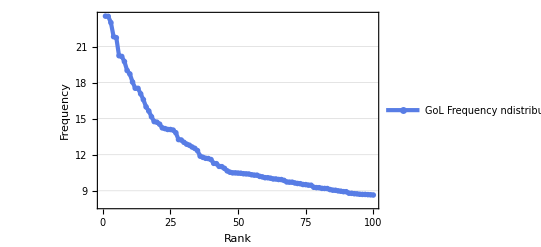

```mathematica
ListLogPlot[N/@(ToExpression[#[[-2]]]&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[])),PlotRange->All,PlotTheme->"Business",Frame->True,PlotLegends->{"GoL Frequency\nndistribution"},Joined->True,FrameLabel->(Style[#,13,Black]&/@{"Rank","Frequency"})]
```

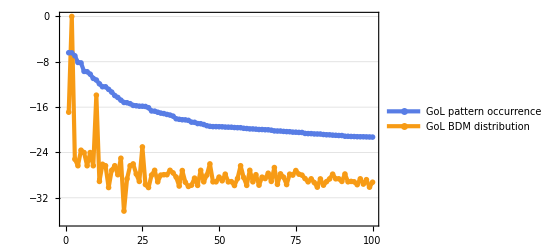

```mathematica
ListLogPlot[({(ToExpression[#[[-2]]]&/@((StringSplit[#,{" "}]&/@(StringSplit[GoLdata,"\n"][[11;;110]]))/. ""->Sequence[]))/10000000000000,(ⅇ^#&/@(-Median/@bdmGoLmotifs[[1;;100]]))10000000000000 }),PlotRange->All,PlotTheme->"Business",Frame->True,PlotLegends->{"GoL pattern\noccurrence","GoL BDM\ndistribution"},Joined->True]
```

Algorithmic distribution of most-likely still structures and most-likely periodic structures:

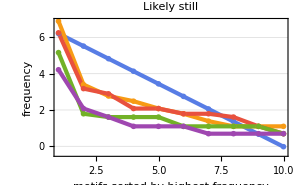
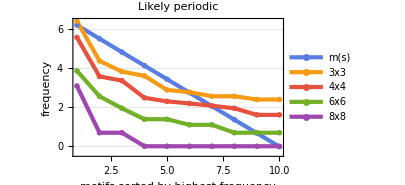

```mathematica
Row[Riffle[{ListLogPlot[Flatten[{{N/@1000Table[1/2^n,{n,1,10}]},#[[1;;10]]&/@dists[[{2,3,5,7}]]},1],PlotRange->All,PlotTheme->"Business",Joined->True,Frame->True,ImageSize->300,PlotLabel->Style["Likely still",14,Black],FrameLabel->{Style["motifs sorted by highest frequency",13],Style["frequency",13]}],ListLogPlot[Flatten[{{N/@1000Table[1/2^n,{n,1,10}]},#[[1;;10]]&/@distperiodic[[{2,3,5,7}]]},1],PlotRange->All,PlotTheme->"Business",Joined->True,PlotLegends->{"m(s)","3x3","4x4","6x6","8x8"},Frame->True,ImageSize->300,PlotLabel->Style["Likely periodic",14,Black],FrameLabel->{Style["motifs sorted by highest frequency",13],Style["frequency",13]}]},"     "]]
```

Given the structured nature of the output of GoL, taking larger blocks reveals this structure, if the pattern were random the block decomposition would have highest block entropy and the distribution of patterns would start flat and remain flat. However, the higher number of structures, the less uniform, but larger blocks will tend to flatten the distributions.

```mathematica
Grid[Partition[Column[Reverse[#],Alignment->Center,Spacings->0]&/@(DeleteDuplicates@SortBy[Thread[{ArrayPlot[ArrayTrim@ImageData[ColorNegate@Binarize@#],ImageSize->If[Max[ImageDimensions[#]]>80,{40,50},{60,60}]]&/@(First/@(If[!Head[#]===List,{#},#]&/@GoLmotifs[[1;;100]])),(Style[#,10,Black]&/@("H = "<>#&/@ToString/@(SetPrecision[#,3]&/@(Median/@entropyGoLmotifs[[1;;100]])))),(Style[#,10,Black]&/@("C = "<>#&/@ToString/@(#&@(Median/@compressGoLmotifs[[1;;100]])))),(Style[#,10,Black]&/@("AP = "<>#&/@ToString/@(SetPrecision[#,3]&/@(Median/@bdmGoLmotifs[[1;;100]]))))}],Last]),10,10,1,""],Dividers->Center]
```

AP = 29.9
C = 104
H = 0.410
-Graphics- | AP = 43.8
C = 120
H = 1.17
-Graphics- | AP = 46.8
C = 96
H = 0.237
-Graphics- | AP = 52.9
C = 128
H = 1.33
-Graphics- | AP = 53.5
C = 120
H = 1.37
-Graphics- | AP = 53.9
C = 120
H = 1.37
-Graphics- | AP = 53.9
C = 120
H = 0.995
-Graphics- | AP = 54.9
C = 128
H = 1.61
-Graphics- | AP = 55.1
C = 128
H = 1.05
-Graphics- | AP = 55.9
C = 144
H = 1.79
-Graphics-
AP = 55.9
C = 144
H = 1.79
-Graphics- | AP = 56.0
C = 124
H = 1.33
-Graphics- | AP = 56.3
C = 128
H = 1.61
-Graphics- | AP = 56.3
C = 136
H = 1.05
-Graphics- | AP = 56.3
C = 136
H = 1.61
-Graphics- | AP = 56.3
C = 128
H = 1.61
-Graphics- | AP = 56.3
C = 136
H = 1.61
-Graphics- | AP = 56.3
C = 136
H = 1.61
-Graphics- | AP = 56.3
C = 136
H = 1.61
-Graphics- | AP = 56.6
C = 160
H = 1.75
-Graphics-
AP = 57.1
C = 136
H = 1.31
-Graphics- | AP = 57.1
C = 136
H = 1.10
-Graphics- | AP = 57.1
C = 136
H = 1.35
-Graphics- | AP = 57.1
C = 152
H = 1.79
-Graphics- | AP = 57.1
C = 144
H = 1.79
-Graphics- | AP = 57.1
C = 144
H = 1.79
-Graphics- | AP = 57.1
C = 160
H = 1.74
-Graphics- | AP = 57.5
C = 152
H = 1.79
-Graphics- | AP = 57.6
C = 152
H = 1.93
-Graphics- | AP = 57.7
C = 152
H = 1.79
-Graphics-
AP = 57.7
C = 148
H = 1.66
-Graphics- | AP = 57.7
C = 152
H = 1.93
-Graphics- | AP = 57.8
C = 152
H = 1.51
-Graphics- | AP = 57.8
C = 152
H = 1.70
-Graphics- | AP = 57.8
C = 176
H = 1.93
-Graphics- | AP = 57.8
C = 160
H = 1.93
-Graphics- | AP = 57.9
C = 152
H = 1.79
-Graphics- | AP = 57.9
C = 152
H = 1.79
-Graphics- | AP = 57.9
C = 152
H = 1.79
-Graphics- | AP = 57.9
C = 152
H = 1.79
-Graphics-
AP = 57.9
C = 152
H = 1.79
-Graphics- | AP = 57.9
C = 160
H = 1.79
-Graphics- | AP = 57.9
C = 152
H = 1.79
-Graphics- | AP = 57.9
C = 152
H = 1.79
-Graphics- | AP = 57.9
C = 144
H = 1.79
-Graphics- | AP = 58.3
C = 176
H = 1.93
-Graphics- | AP = 58.3
C = 160
H = 1.37
-Graphics- | AP = 58.3
C = 176
H = 2.04
-Graphics- | AP = 58.3
C = 176
H = 1.37
-Graphics- | AP = 58.3
C = 160
H = 1.52
-Graphics-
AP = 58.5
C = 152
H = 1.51
-Graphics- | AP = 58.5
C = 152
H = 1.51
-Graphics- | AP = 58.5
C = 160
H = 1.56
-Graphics- | AP = 58.5
C = 176
H = 1.93
-Graphics- | AP = 58.6
C = 176
H = 1.93
-Graphics- | AP = 58.6
C = 176
H = 1.93
-Graphics- | AP = 58.6
C = 176
H = 1.93
-Graphics- | AP = 58.6
C = 176
H = 1.70
-Graphics- | AP = 58.6
C = 160
H = 1.51
-Graphics- | AP = 58.6
C = 176
H = 1.93
-Graphics-
AP = 58.6
C = 176
H = 1.93
-Graphics- | AP = 58.7
C = 192
H = 1.68
-Graphics- | AP = 58.9
C = 176
H = 1.93
-Graphics- | AP = 59.0
C = 176
H = 1.93
-Graphics- | AP = 59.0
C = 176
H = 1.93
-Graphics- | AP = 59.0
C = 176
H = 1.93
-Graphics- | AP = 59.0
C = 176
H = 1.93
-Graphics- | AP = 59.0
C = 176
H = 1.75
-Graphics- | AP = 59.1
C = 176
H = 1.93
-Graphics- | AP = 59.1
C = 176
H = 1.93
-Graphics-
AP = 59.1
C = 176
H = 1.37
-Graphics- | AP = 59.1
C = 192
H = 1.58
-Graphics- | AP = 59.1
C = 192
H = 1.89
-Graphics- | AP = 59.1
C = 176
H = 1.89
-Graphics- | AP = 59.1
C = 176
H = 1.83
-Graphics- | AP = 59.1
C = 176
H = 1.68
-Graphics- | AP = 59.1
C = 176
H = 1.68
-Graphics- | AP = 59.1
C = 176
H = 1.68
-Graphics- | AP = 59.1
C = 176
H = 1.83
-Graphics- | AP = 59.2
C = 176
H = 1.75
-Graphics-
AP = 59.2
C = 192
H = 1.93
-Graphics- | AP = 59.2
C = 176
H = 1.75
-Graphics- | AP = 59.5
C = 192
H = 1.74
-Graphics- | AP = 59.6
C = 192
H = 2.04
-Graphics- | AP = 59.6
C = 208
H = 1.89
-Graphics- | AP = 59.6
C = 192
H = 1.71
-Graphics- | AP = 59.6
C = 192
H = 1.81
-Graphics- | AP = 59.7
C = 192
H = 1.37
-Graphics- | AP = 59.7
C = 192
H = 1.68
-Graphics- | AP = 59.7
C = 192
H = 1.83
-Graphics-
AP = 59.7
C = 192
H = 2.04
-Graphics- | AP = 59.7
C = 192
H = 1.83
-Graphics- | AP = 59.8
C = 192
H = 0.995
-Graphics- | AP = 59.9
C = 208
H = 1.76
-Graphics- | AP = 59.9
C = 192
H = 1.52
-Graphics- | AP = 60.1
C = 208
H = 1.74
-Graphics- | AP = 60.1
C = 208
H = 2.04
-Graphics- | AP = 60.1
C = 192
H = 2.04
-Graphics- | AP = 60.1
C = 192
H = 1.74
-Graphics- | AP = 64.3
C = 384
H = 1.48
-Graphics-

Dynamic Complexity

```mathematica
GameOfLife={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
```

```mathematica
Row@Riffle[ArrayPlot[#,ImageSize->40,Mesh->True]&/@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,1,0},{0,0,1},{1,1,1}},0},8],"   "]
```

-Graphics-   -Graphics-   -Graphics-   -Graphics-   -Graphics-   -Graphics-   -Graphics-   -Graphics-   -Graphics-

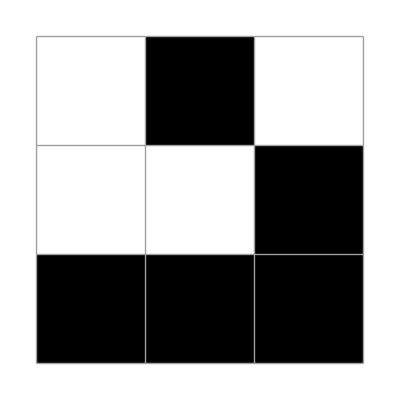

```mathematica
ArrayPlot[ArrayTrim[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,1,0},{0,0,1},{1,1,1}},0},36][[1]]],Mesh->All,ImageSize->Tiny]
```

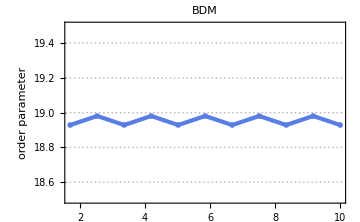

```mathematica
ListLinePlot[N/@BDM/@ArrayTrim/@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,1,0},{0,0,1},{1,1,1}},0},10],PlotMarkers->{Automatic,Large},Joined->True,Frame->True,ImageSize->Medium,PlotTheme->"Business",PlotRange->{18.5,19.5},PlotLabel->Style["BDM",16,Black],FrameLabel->{Row[Riffle[ArrayPlot[#,ImageSize->30]&/@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,1,0},{0,0,1},{1,1,1}},0},9]," "]],Style["order parameter",14,Black]},DataRange->{1.7,10}]
```

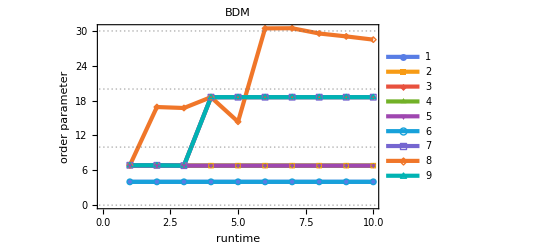

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]>2)&&(Count[Flatten[#],1]<5)&]},ListPlot[N/@Map[BDM,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},9]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[9]}]))),PlotLabel->Style["BDM",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

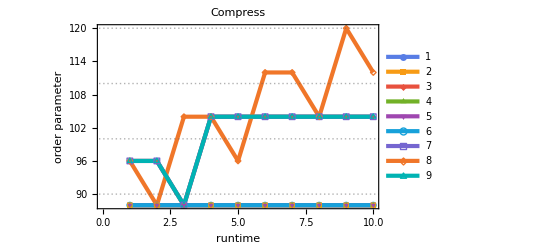

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]>2)&&(Count[Flatten[#],1]<5)&]},ListPlot[N/@Map[ByteCount[Compress[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},9]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[9]}]))),PlotLabel->Style["Compress",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

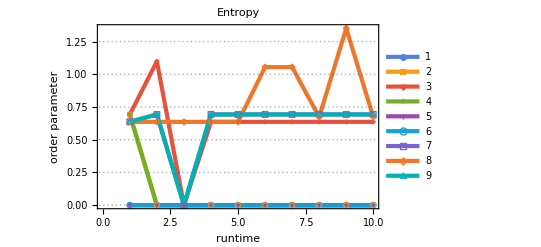

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]>2)&&(Count[Flatten[#],1]<5)&]},ListPlot[N/@Map[N[Entropy[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},9]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[9]}]))),PlotLabel->Style["Entropy",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

```mathematica
Grid[Partition[Row/@(Riffle[#," "]&/@(Flatten/@Thread[{Range[9],Map[ArrayPlot[#,ImageSize->{30,30},Mesh->All]&,Map[ArrayTrim,(CellularAutomaton[GameOfLife,{#,0},9]&/@Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]>2)&&(Count[Flatten[#],1]<5)&]),{2}],{2}]}])),1,1,1,""],Dividers->Center]
```

1 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
2 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
3 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
4 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
5 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
6 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
7 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
8 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
9 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-

```mathematica
Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]]
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,1}},{{0,0,0},{0,0,0},{0,1,1}},{{0,0,0},{0,0,0},{1,1,1}},{{0,0,0},{0,0,1},{0,0,1}},{{0,0,0},{0,0,1},{0,1,1}},{{0,0,0},{0,0,1},{1,1,1}},{{0,0,0},{0,1,1},{0,0,1}},{{0,0,0},{0,1,1},{0,1,1}},{{0,0,0},{0,1,1},{1,1,1}},{{0,0,0},{1,1,1},{1,1,1}},{{0,0,1},{0,0,1},{0,0,1}},{{0,0,1},{0,0,1},{0,1,1}},{{0,0,1},{0,0,1},{1,1,1}},{{0,0,1},{0,1,1},{0,0,1}},{{0,0,1},{0,1,1},{0,1,1}},{{0,0,1},{0,1,1},{1,1,1}},{{0,0,1},{1,1,1},{1,1,1}},{{0,1,1},{0,0,1},{0,0,1}},{{0,1,1},{0,0,1},{0,1,1}},{{0,1,1},{0,0,1},{1,1,1}},{{0,1,1},{0,1,1},{0,0,1}},{{0,1,1},{0,1,1},{0,1,1}},{{0,1,1},{0,1,1},{1,1,1}},{{0,1,1},{1,1,1},{1,1,1}},{{1,1,1},{1,1,1},{1,1,1}}}

```mathematica
cases=Select[Rest[(Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]==6)&]
```

{{{0,0,0},{1,1,1},{1,1,1}},{{0,0,1},{0,1,1},{1,1,1}},{{0,1,1},{0,0,1},{1,1,1}},{{0,1,1},{0,1,1},{0,1,1}}}

```mathematica
ArrayPlot[#,ImageSize->{40,40},Mesh->All]&/@ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},28]&/@cases
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

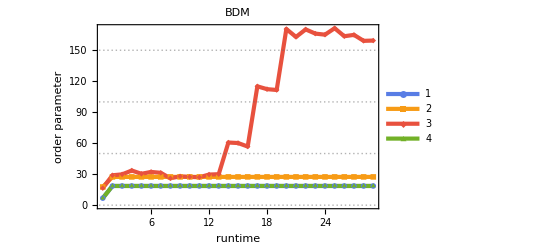

```mathematica
ListPlot[N/@Map[N[BDM[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},28]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[4]}]))),PlotRange->All,PlotLabel->Style["BDM",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]
```

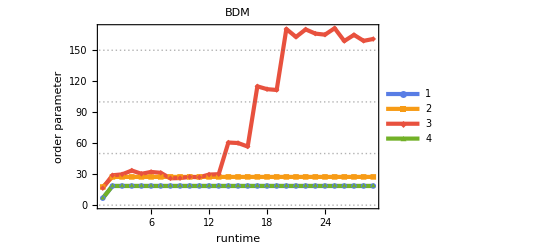

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]==6)&]},ListPlot[N/@Map[N[BDM[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},28]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[4]}]))),PlotRange->All,PlotLabel->Style["BDM",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

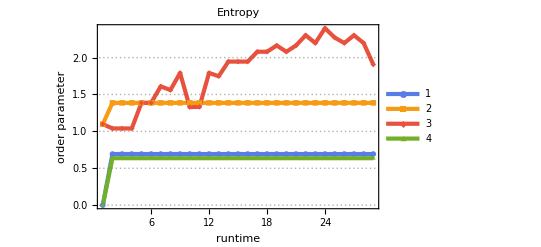

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]==6)&]},ListPlot[N/@Map[N[Entropy[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},28]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[4]}]))),PlotRange->All,PlotLabel->Style["Entropy",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

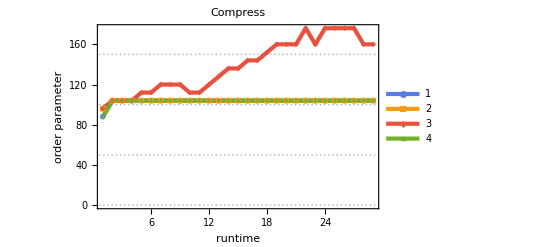

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]==6)&]},ListPlot[N/@Map[ByteCount[Compress[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},28]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[4]}]))),PlotRange->All,PlotLabel->Style["Compress",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

```mathematica
Grid[Partition[Row/@(Riffle[#," "]&/@(Flatten/@Thread[{Range[4],Map[ArrayPlot[#,ImageSize->{40,40},Mesh->All]&,Map[ArrayTrim,(CellularAutomaton[GameOfLife,{#,0},15]&/@Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]==6)&]),{2}],{2}]}])),1,1,1,""],Dividers->Center]
```

1 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
2 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
3 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
4 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-

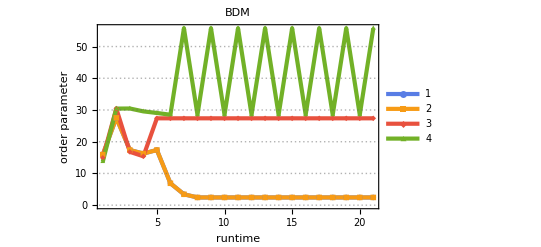

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]>6)&]},ListPlot[N/@Map[N[BDM[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},20]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[4]}]))),PlotRange->All,PlotLabel->Style["BDM",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

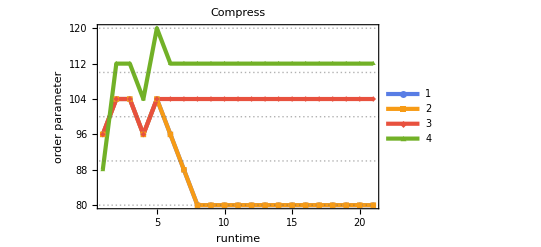

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]>6)&]},ListPlot[N/@Map[ByteCount[Compress[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},20]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[4]}]))),PlotRange->All,PlotLabel->Style["Compress",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

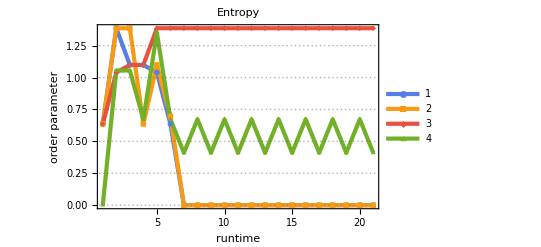

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]>6)&]},ListPlot[N/@Map[N[Entropy[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},20]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[4]}]))),PlotRange->All,PlotLabel->Style["Entropy",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

```mathematica
Grid[Partition[(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{Range[4],(Map[ArrayPlot[#,ImageSize->{40,40},Mesh->All]&,Map[ArrayTrim,(CellularAutomaton[GameOfLife,{#,0},15]&/@Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{3,3}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]>6)&]),{2}],{2}])}]))),1,1,1,""],Dividers->Center]
```

1 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
2 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
3 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
4 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-

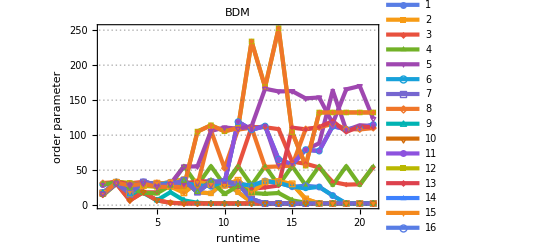

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{4,4}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]>8)&&(Count[Flatten[#],1]<10)&]},ListPlot[N/@Map[N[BDM[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},20]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[23]}]))),PlotRange->All,PlotLabel->Style["BDM",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

```mathematica
Grid[Partition[Row/@(Riffle[#," "]&/@(Flatten/@Thread[{Range[23],Map[ArrayPlot[#,ImageSize->{30,30},Mesh->If[(Length[#]>6)||(Length[Transpose[#]]>6),None,All]]&,Map[ArrayTrim,(CellularAutomaton[GameOfLife,{#,0},15]&/@Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{4,4}])],{2}]])/. {}->{{0}}],(Count[Flatten[#],1]>8)&&(Count[Flatten[#],1]<10)&]),{2}],{2}]}])),1,1,1,""],Dividers->Center]
```

1 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
2 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
3 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
4 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
5 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
6 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
7 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
8 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
9 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
10 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
11 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
12 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
13 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
14 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
15 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
16 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
17 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
18 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
19 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
20 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
21 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
22 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
23 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-

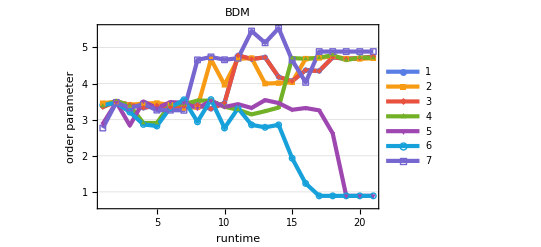

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{4,4}])],{2}]])/. {}->{{0}}],(Count[#[[3]],0]>1)&&(Count[Flatten[#],1]==9)&&(Length[#]==4)&&(Length[Transpose[#]]>2)&]},ListLogPlot[N/@Map[N[BDM[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},20]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[7]}]))),PlotRange->All,PlotLabel->Style["BDM",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

```mathematica
Grid[Partition[Row/@(Riffle[#," "]&/@(Flatten/@Thread[{Range[7],Map[ArrayPlot[#,ImageSize->{40,40},Mesh->If[(Length[#]>6)||(Length[Transpose[#]]>6),None,All]]&,Map[ArrayTrim,(CellularAutomaton[GameOfLife,{#,0},15]&/@Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{4,4}])],{2}]])/. {}->{{0}}],(Count[#[[3]],0]>1)&&(Count[Flatten[#],1]==9)&&(Length[#]==4)&&(Length[Transpose[#]]>2)&]),{2}],{2}]}])),1,1,1,""],Dividers->Center]
```

1 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
2 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
3 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
4 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
5 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
6 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-
7 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-

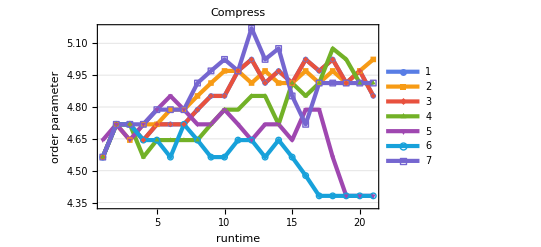

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{4,4}])],{2}]])/. {}->{{0}}],(Count[#[[3]],0]>1)&&(Count[Flatten[#],1]==9)&&(Length[#]==4)&&(Length[Transpose[#]]>2)&]},ListLogPlot[N/@Map[ByteCount[Compress[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},20]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[7]}]))),PlotRange->All,PlotLabel->Style["Compress",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

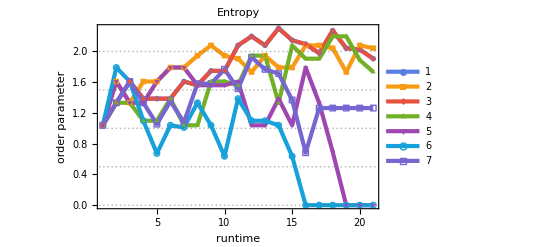

```mathematica
Module[{cases=Select[Rest[(ArrayTrim/@Union[Map[Sort,Sort[Sort/@(Tuples[{0,1},{4,4}])],{2}]])/. {}->{{0}}],(Count[#[[3]],0]>1)&&(Count[Flatten[#],1]==9)&&(Length[#]==4)&&(Length[Transpose[#]]>2)&]},ListPlot[N/@Map[N[Entropy[#]]&,(ArrayTrim/@CellularAutomaton[GameOfLife,{#,0},20]&/@cases)/.{}->{{0}},{2}],PlotMarkers->{Automatic,Large},Joined->True,PlotTheme->"Business",Frame->True,PlotLegends->(Row/@(Riffle[#," "]&/@(Flatten/@Thread[{(ArrayPlot[#,ImageSize->{20,20},Mesh->All]&/@cases),Range[7]}]))),PlotRange->All,PlotLabel->Style["Entropy",16,Black],FrameLabel->{Style["runtime",14,Black],Style["order parameter",14,Black]}]]
```

### Glider-based particle collider

```mathematica
ArrayPlot[#,ImageSize->40,Mesh->True]&/@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,1,0},{0,0,1},{1,1,1}},0},8]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
glider={{0,1,0},{0,0,1},{1,1,1}};
```

```mathematica
glider2=Reverse[{{0,1,0},{0,0,1},{1,1,1}}];
```

```mathematica
antiglider=Reverse[Reverse/@{{0,1,0},{0,0,1},{1,1,1}}];
```

```mathematica
antiglider2=Reverse/@{{0,1,0},{0,0,1},{1,1,1}};
```

```mathematica
ParticleGenerator[particle_,coordinates_,initspace_]:=If[particle==="glider",ReplacePart[initspace,Rule@@@Thread[{Position[glider,1],1}]],If[particle==="antiglider",ReplacePart[initspace,Rule@@@Thread[{-1Position[glider,1],1}]],If[particle==="glider2",ReplacePart[initspace,Rule@@@Thread[{{-1#[[1]],#[[2]]}&/@Position[glider,1],1}]],If[particle==="antiglider2",ReplacePart[initspace,Rule@@@Thread[{{#[[1]],-1#[[2]]}&/@Position[glider,1],1}]]]]]]
```

Free particle:

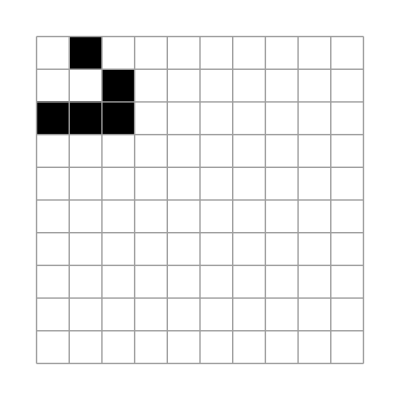

```mathematica
ArrayPlot[ParticleGenerator["glider",{1,1},ConstantArray[0,{10,10}]],ImageSize->Tiny,Mesh->All]
```

2-particle front collision:

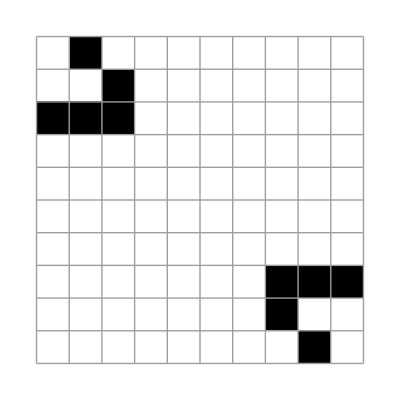

```mathematica
ArrayPlot[ParticleGenerator["antiglider",{10,10},ParticleGenerator["glider",{1,1},ConstantArray[0,{10,10}]]],ImageSize->Tiny,Mesh->All]
```

2-particle side collision:

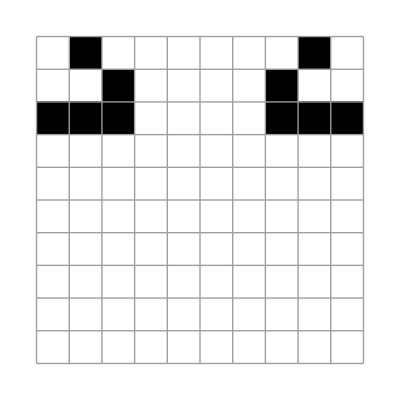

```mathematica
ArrayPlot[ParticleGenerator["antiglider2",{10,10},ParticleGenerator["glider",{1,1},ConstantArray[0,{10,10}]]],ImageSize->Tiny,Mesh->All]
```

3-particle collision:

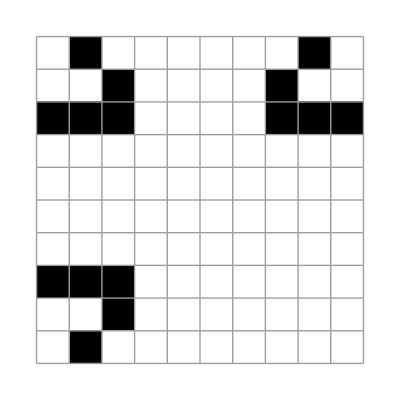

```mathematica
ArrayPlot[ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{10,10},ParticleGenerator["glider",{1,1},ConstantArray[0,{10,10}]]]],ImageSize->Tiny,Mesh->All]
```

Multiple collision:

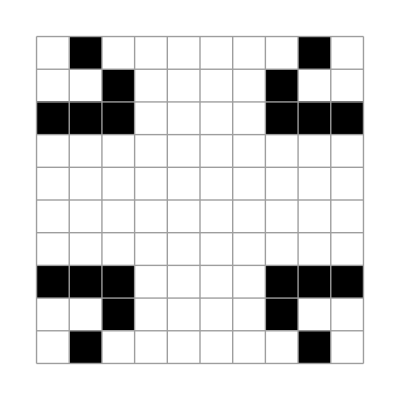

```mathematica
ArrayPlot[ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{10,10},ParticleGenerator["glider",{1,1},ConstantArray[0,{10,10}]]]]],ImageSize->Tiny,Mesh->All]
```

### Complexity collider tracker:

```mathematica
ParticleCollider[gridsize_]:=ParticleGenerator["antiglider",gridsize,ParticleGenerator["glider",{1,1},ConstantArray[0,gridsize]]]
```

```mathematica
Manipulate[ArrayPlot[ArrayTrim[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleCollider[{10,10}],0},i]],Mesh->All,ImageSize->Tiny],{i,0,20,1}]
```

```mathematica
Manipulate[ArrayPlot[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider2",{1,1},ParticleGenerator["glider",{1,1},ParticleGenerator["antiglider2",{8 2,9 2},ParticleGenerator["glider",{1,1},ConstantArray[0,{8 2,9 2}]]]]],0},i],Mesh->All,ImageSize->Tiny],{i,0,50,1}]
```

```mathematica
Manipulate[ArrayPlot[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider",{1,1},ParticleGenerator["antiglider2",{8 2,9 2},ParticleGenerator["glider",{1,1},ConstantArray[0,{8 2,9 2}]]]]],0},i],Mesh->All,ImageSize->Tiny],{i,0,30,1}]
```

```mathematica
Manipulate[ArrayPlot[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{8 2,9 2},ParticleGenerator["glider",{1,1},ConstantArray[0,{8 2,9 2}]]]]],0},i],Mesh->All,ImageSize->Tiny],{i,0,30,1}]
```

```mathematica
Manipulate[ArrayPlot[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider",{1,1},ParticleGenerator["antiglider",{8 2,9 2},ParticleGenerator["glider",{1,1},ConstantArray[0,{8 2,9 2}]]]]],0},i],Mesh->All,ImageSize->Tiny],{i,0,30,1}]
```

Jump at time 5 is because of the collider detection resolution of 4x4 and is the moment in which both particles enter the observation sliding window of 4x4. Before time 5 particles are considered individually showing no significant increase in complexity.

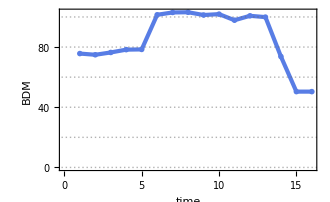

```mathematica
ListPlot[BDM/@Table[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleCollider[{10,10}],0},i],{i,0,15,1}],PlotTheme->"Business",Joined->True,Frame->True,FrameLabel->(Style[#,14,Black]&/@{"time","BDM"}),ImageSize->330]
```

```mathematica
Grid[Partition[Column[#,Alignment->Center]&/@Table[{i,ArrayPlot[#,ImageSize->40]&@Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleCollider[{10,10}],0},i]},{i,0,15,1}],8],Dividers->Center]
```

0
-Graphics- | 1
-Graphics- | 2
-Graphics- | 3
-Graphics- | 4
-Graphics- | 5
-Graphics- | 6
-Graphics- | 7
-Graphics-
8
-Graphics- | 9
-Graphics- | 10
-Graphics- | 11
-Graphics- | 12
-Graphics- | 13
-Graphics- | 14
-Graphics- | 15
-Graphics-

```mathematica
Manipulate[ArrayPlot[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{8,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{8,9}]]]],0},i],Mesh->All,ImageSize->Tiny],{i,0,50,1}]
```

:

```mathematica
Manipulate[ArrayPlot[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{9,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{9,9}]]]]],0},i],Mesh->All,ImageSize->Tiny],{i,0,50,1}]
```

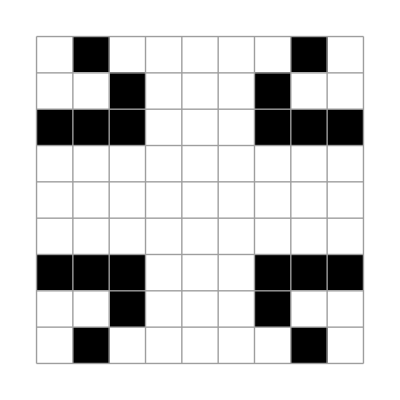
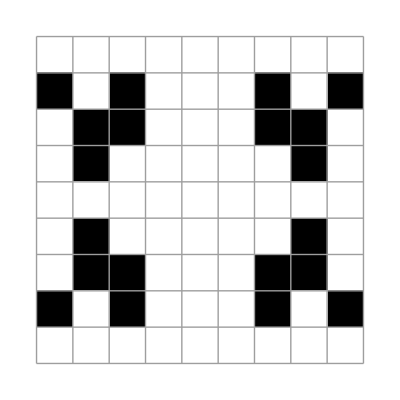
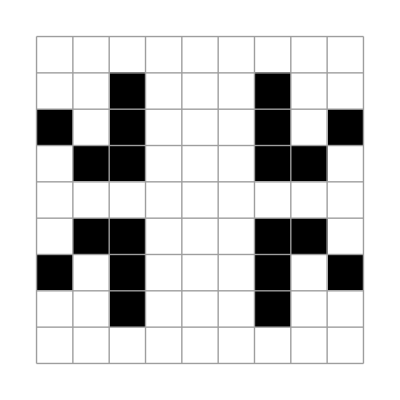
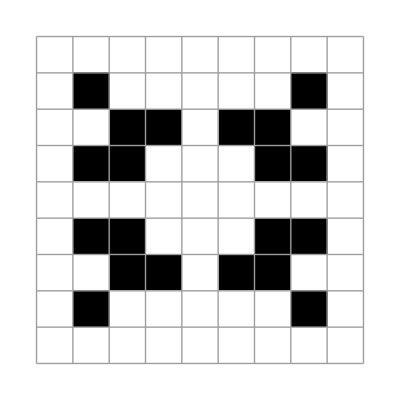
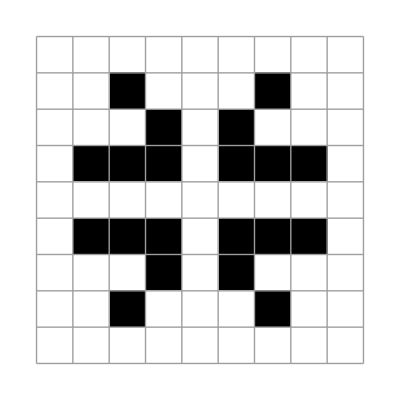
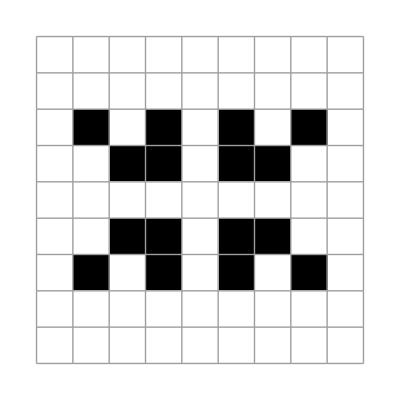
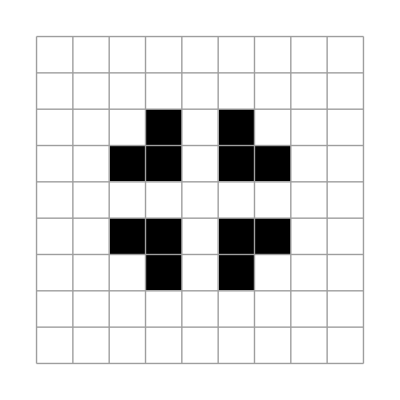
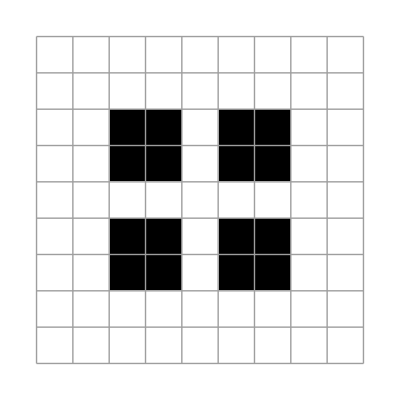
0
-Graphics- | 1
-Graphics- | 2
-Graphics- | 3
-Graphics-
4
-Graphics- | 5
-Graphics- | 6
-Graphics- | 7
-Graphics-

```mathematica
Grid[Partition[Table[Column[{i,ArrayPlot[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{9,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{9,9}]]]]],0},i],Mesh->All,ImageSize->Tiny]},Alignment->Center],{i,0,7,1}],4]]
```

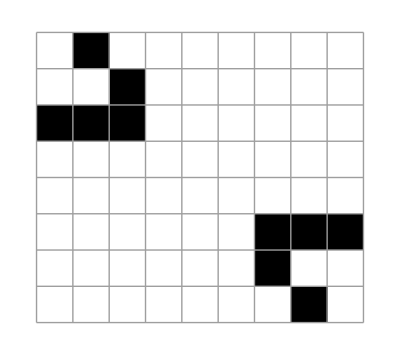
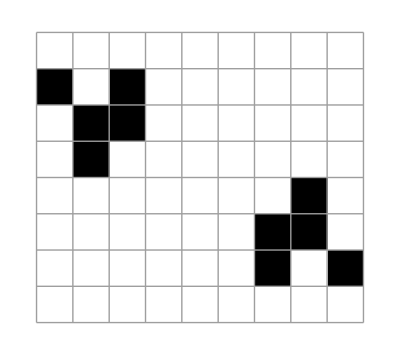
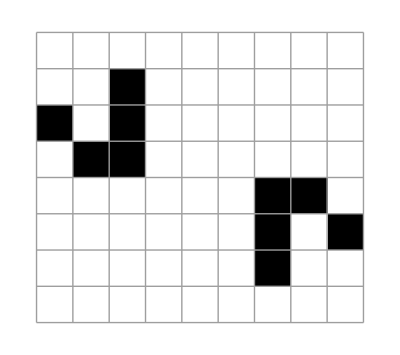
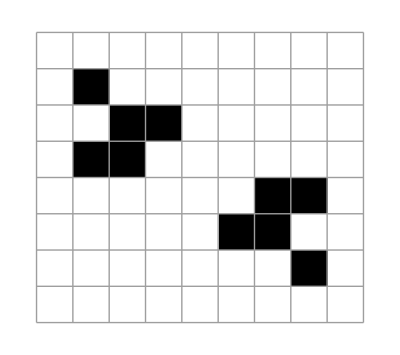
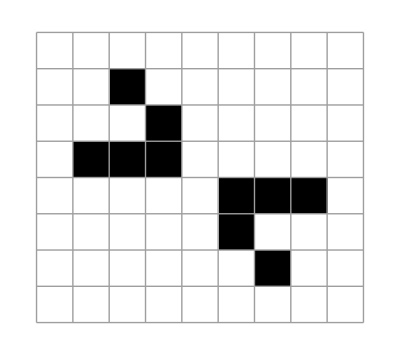
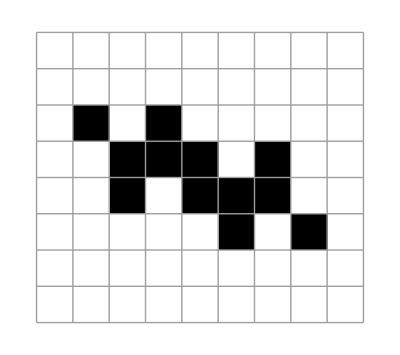
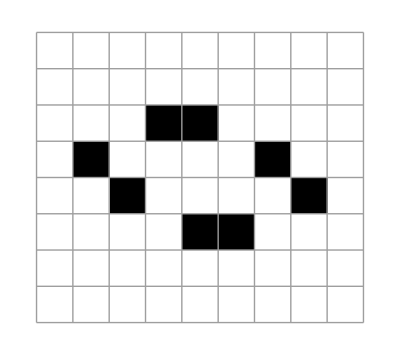
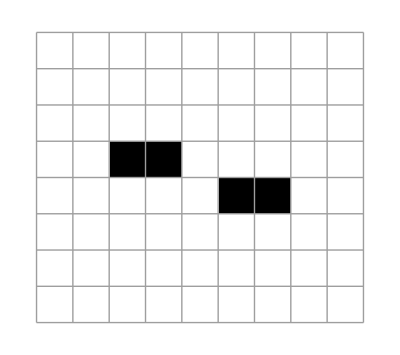
0
-Graphics- | 1
-Graphics- | 2
-Graphics- | 3
-Graphics- | 4
-Graphics-
5
-Graphics- | 6
-Graphics- | 7
-Graphics- | 8
-Graphics- | 9
-Graphics-

```mathematica
Grid[Partition[Table[Column[{i,ArrayPlot[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider",{1,1},ParticleGenerator["antiglider",{8,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{8,9}]]]]],0},i],Mesh->All,ImageSize->Tiny]},Alignment->Center],{i,0,9,1}],5]]
```

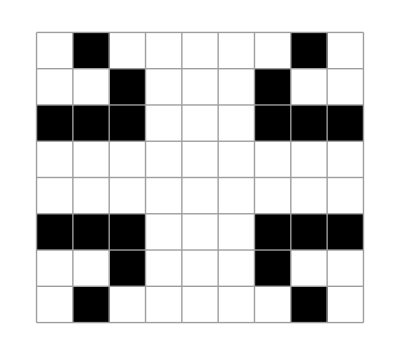
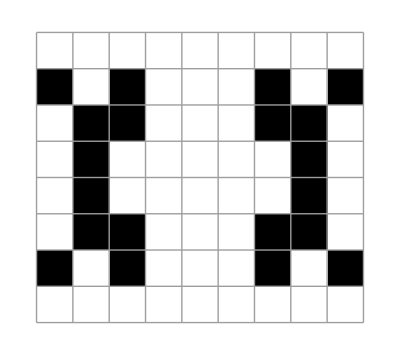
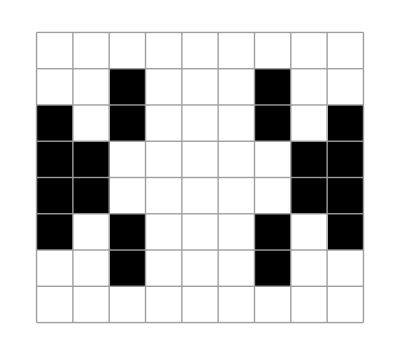
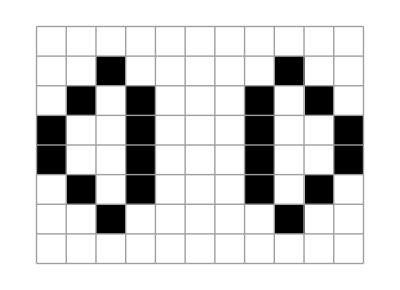
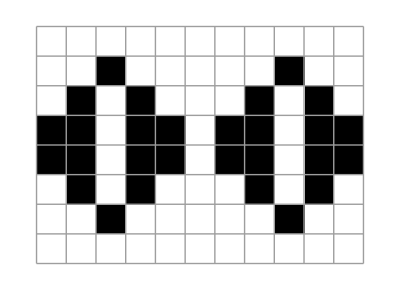
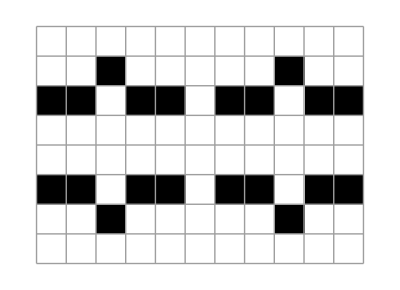
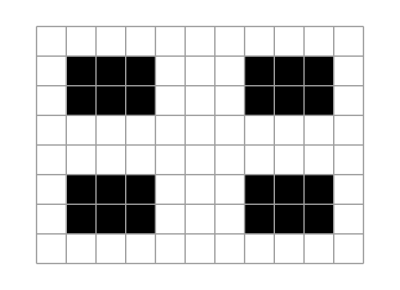
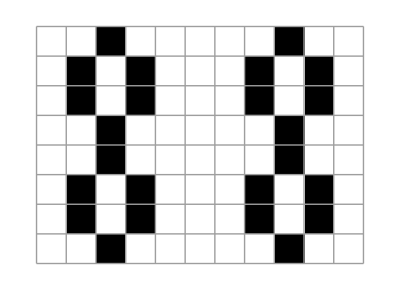
0
-Graphics- | 1
-Graphics- | 2
-Graphics- | 3
-Graphics- | 4
-Graphics- | 5
-Graphics- | 6
-Graphics- | 7
-Graphics- | 8
-Graphics-
9
-Graphics- | 10
-Graphics- | 11
-Graphics- | 12
-Graphics- | 13
-Graphics- | 14
-Graphics- | 15
-Graphics- | 16
-Graphics- | 17
-Graphics-
18
-Graphics- | 19
-Graphics- | 20
-Graphics- | 21
-Graphics- | 22
-Graphics- | 23
-Graphics- | 24
-Graphics- | 25
-Graphics- | 26
-Graphics-
27
-Graphics- | 28
-Graphics- | 29
-Graphics- | 30
-Graphics- | 31
-Graphics- | 32
-Graphics- | 33
-Graphics- | 34
-Graphics- | 35
-Graphics-
36
-Graphics- | 37
-Graphics- | 38
-Graphics- | 39
-Graphics- | 40
-Graphics- | 41
-Graphics- | 42
-Graphics- | 43
-Graphics- | 44
-Graphics-
45
-Graphics- | 46
-Graphics- | 47
-Graphics- | 48
-Graphics- | 49
-Graphics- | 50
-Graphics- | 51
-Graphics- | 52
-Graphics- | 53
-Graphics-

```mathematica
Grid[Partition[Table[Column[{i,ArrayPlot[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{8,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{8,9}]]]]],0},i],Mesh->All,ImageSize->Tiny]},Alignment->Center],{i,0,60,1}],9]]
```

Annihilation v new unstable particle generation:

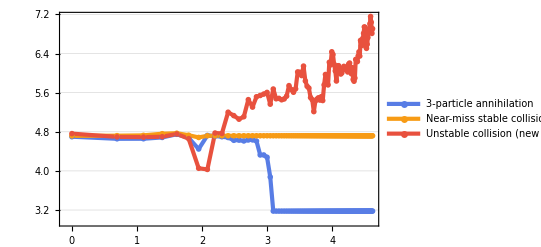

```mathematica
ListLogLogPlot[{BDM/@Table[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{8,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{8,9}]]]],0},i],{i,0,100,1}],BDM/@Table[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{9,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{9,9}]]]]],0},i],{i,0,100,1}],BDM/@Table[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{8,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{8,9}]]]]],0},i],{i,0,100,1}]},PlotTheme->"Business",Joined->True,PlotLegends->{"3-particle\nannihilation","Near-miss\nstable collision","Unstable collision\n(new particles)"}]
```

Definition of collision: when the change of the state of cells in the causal vicinity (with ratio equal to the CA neighbourhood) affects another local pattern.

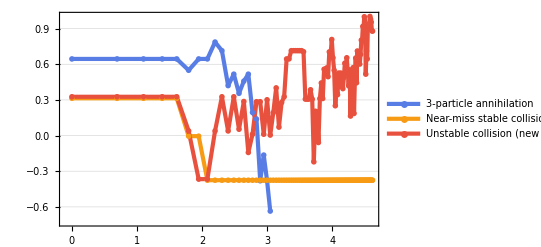

```mathematica
ListLogLogPlot[{Entropy/@Table[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{8,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{8,9}]]]],0},i],{i,0,100,1}],Entropy/@Table[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{9,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{9,9}]]]]],0},i],{i,0,100,1}],Entropy/@Table[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{8,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{8,9}]]]]],0},i],{i,0,100,1}]},PlotTheme->"Business",Joined->True,PlotLegends->{"3-particle\nannihilation","Near-miss\nstable collision","Unstable collision\n(new particles)"}]
```

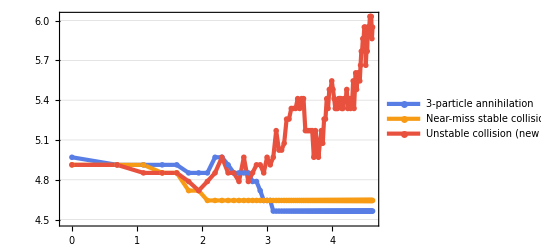

```mathematica
ListLogLogPlot[{ByteCount/@Compress/@Table[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{8,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{8,9}]]]],0},i],{i,0,100,1}],ByteCount/@Compress/@Table[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{9,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{9,9}]]]]],0},i],{i,0,100,1}],ByteCount/@Compress/@Table[Last@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{8,9},ParticleGenerator["glider",{1,1},ConstantArray[0,{8,9}]]]]],0},i],{i,0,100,1}]},PlotTheme->"Business",Joined->True,PlotLegends->{"3-particle\nannihilation","Near-miss\nstable collision","Unstable collision\n(new particles)"}]
```

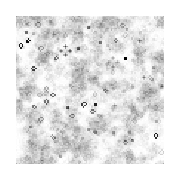
-Graphics-   -Graphics-   -Graphics-

```mathematica
Module[{randinit=RandomInteger[1,{100,100}]},Row[Riffle[{ArrayPlot[Mean@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},randinit,100],ImageSize->Small],ArrayPlot[Map[If[TrueQ[#>.5],1,0]&,(N/@(Mean@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},randinit,50])),{2}],ImageSize->Small],ArrayPlot[Map[If[TrueQ[#>.3]&&TrueQ[#<.6],1,0]&,(N/@(Mean@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},randinit,50])),{2}],ImageSize->Small]},"   "]]]
```

```mathematica
dists=Table[Last/@({#[[1]],(7-Length[Union[{#[[1,1]],Reverse/@#[[1,1]],Reverse[#[[1,1]]],Reverse[Reverse/@#[[1,1]]],Transpose[#[[1,1]]],Reverse/@Transpose[#[[1,1]]],Reverse[Reverse/@Transpose[#[[1,1]]]]}]])#[[2]]}&/@Reverse[SortBy[Tally[First/@Sort/@Map[ArrayPlot[#,ImageSize->40]&,({#,Reverse@#,Reverse/@#,Reverse[Reverse/@#],Transpose[#]}&/@Flatten[(Partition[Map[If[TrueQ[#>.5],1,0]&,(N/@(Mean@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},RandomInteger[1,{100,100}],50])),{2}],{i,i}]),1]),{2}]],Last]]),{i,2,8,1}];
```

```mathematica
distperiodic=Table[Last/@({#[[1]],(7-Length[Union[{#[[1,1]],Reverse/@#[[1,1]],Reverse[#[[1,1]]],Reverse[Reverse/@#[[1,1]]],Transpose[#[[1,1]]],Reverse/@Transpose[#[[1,1]]],Reverse[Reverse/@Transpose[#[[1,1]]]]}]])#[[2]]}&/@Reverse[SortBy[Tally[First/@Sort/@Map[ArrayPlot[#,ImageSize->40]&,({#,Reverse@#,Reverse/@#,Reverse[Reverse/@#],Transpose[#]}&/@Flatten[(Partition[Map[If[TrueQ[#>.3]&&TrueQ[#<.5],1,0]&,(N/@(Mean@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},RandomInteger[1,{100,100}],50])),{2}],{i,i}]),1]),{2}]],Last]]),{i,2,8,1}];
```

```mathematica
Grid[Partition[ArrayPlot[#,ImageSize->{60,60}]&/@(((CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{7 2,7 2},ParticleGenerator["glider",{1,1},ConstantArray[0,{7 2,7 2}]]]]],0},20]))),10],Spacings->{.5,.8},Dividers->{False, All}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Partition[ArrayPlot[#,ImageSize->{60,60}]&/@(((CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{8 2,9 2},ParticleGenerator["glider",{1,1},ConstantArray[0,{8 2,9 2}]]]]],0},40]))),10],Spacings->{.5,.8},Dividers->{False, All}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Partition[ArrayPlot[#,ImageSize->{60,60}]&/@(((CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",{9 2,9 2},ParticleGenerator["glider",{1,1},ConstantArray[0,{9 2,9 2}]]]]],0},30]))),10],Spacings->{.5,.8},Dividers->{False, All}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Mean distribution of all possible qualitative different interactions among 4 particles:

```mathematica
Row[Riffle[Table[Column[{ToString[#[[1]]]<>" x "<>ToString[#[[2]]],ArrayPlot[Mean[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",gridsize,ParticleGenerator["glider",{1,1},ConstantArray[0,gridsize]]]]],0},300]],ImageSize->100]},Alignment->Center]&@gridsize,{gridsize,Reverse[Subsets[Range[12,20],{2}][[{1,2,4,5,9}]]]}],"   "]]
```

13 x 14
-Graphics-   12 x 17
-Graphics-   12 x 16
-Graphics-   12 x 14
-Graphics-   12 x 13
-Graphics-

```mathematica
bdmcollidingruns=Table[N/@BDM/@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",gridsize,ParticleGenerator["glider",{1,1},ConstantArray[0,gridsize]]]]],0},200],{gridsize,Subsets[Range[12,20],{2}][[{1,2,4,5,9}]]}];
```

```mathematica
bdmcollidingallruns=Table[N/@BDM/@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",gridsize,ParticleGenerator["glider",{1,1},ConstantArray[0,gridsize]]]]],0},200],{gridsize,Subsets[Range[12,20],{2}]}];
```

```mathematica
entropycollidingruns=Table[N/@Entropy/@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",gridsize,ParticleGenerator["glider",{1,1},ConstantArray[0,gridsize]]]]],0},200],{gridsize,Subsets[Range[12,20],{2}][[{1,2,4,5,9}]]}];
```

```mathematica
entropycollidingallruns=Table[N/@Entropy/@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",gridsize,ParticleGenerator["glider",{1,1},ConstantArray[0,gridsize]]]]],0},200],{gridsize,Subsets[Range[12,20],{2}]}];
```

```mathematica
compresscollidingruns=Table[ByteCount/@Compress/@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",gridsize,ParticleGenerator["glider",{1,1},ConstantArray[0,gridsize]]]]],0},200],{gridsize,Subsets[Range[12,20],{2}][[{1,2,4,5,9}]]}];
```

```mathematica
compresscollidingallruns=Table[ByteCount/@Compress/@CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ParticleGenerator["antiglider",{1,1},ParticleGenerator["glider2",{1,1},ParticleGenerator["antiglider2",gridsize,ParticleGenerator["glider",{1,1},ConstantArray[0,gridsize]]]]],0},200],{gridsize,Subsets[Range[12,20],{2}]}];
```

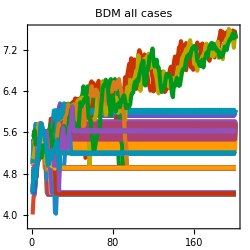
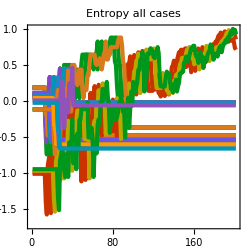
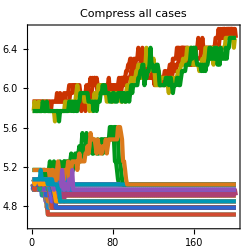

```mathematica
Row[{ListLogPlot[bdmcollidingallruns,PlotRange->All,PlotTheme->"Web",AspectRatio->1,ImageSize->250,Joined->True,PlotLabel->Style["BDM all cases",14,Black]],ListLogPlot[entropycollidingallruns,PlotRange->All,PlotTheme->"Web",AspectRatio->1,ImageSize->250,Joined->True,PlotLabel->Style["Entropy all cases",14,Black]],ListLogPlot[compresscollidingallruns,PlotRange->All,PlotTheme->"Web",AspectRatio->1,ImageSize->250,Joined->True,PlotLabel->Style["Compress all cases",14,Black]]}]
```

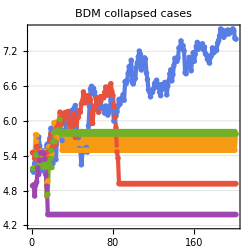
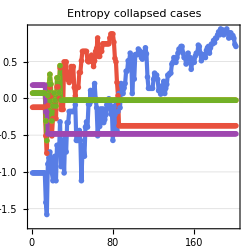
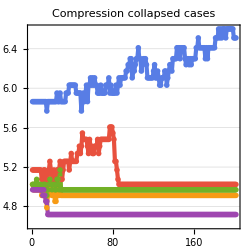

```mathematica
Row[{ListLogPlot[bdmcollidingruns,PlotRange->All,PlotTheme->"Business",AspectRatio->1,ImageSize->250,Joined->True,PlotLabel->Style["BDM collapsed cases",14,Black]],ListLogPlot[entropycollidingruns,PlotRange->All,PlotTheme->"Business",AspectRatio->1,ImageSize->250,Joined->True,PlotLabel->Style["Entropy collapsed cases",14,Black]],ListLogPlot[compresscollidingruns,PlotRange->All,PlotTheme->"Business",AspectRatio->1,ImageSize->250,Joined->True,PlotLabel->Style["Compression collapsed cases",14,Black]]}]
```